## VertexOutwardVector-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 12:31:41
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

Create a tissue with a point and an edge that aren't used.

There are 8 cells in the tissue.

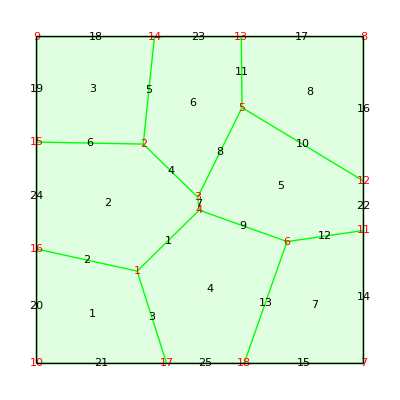

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Q=Tissue2DTissue[q]; 
Print["There are ", NTissueCells[Q], " cells in the tissue."];  
ShowTissue[Q, "CellNumbers"-> True, Frame-> False, "EdgeStyles"-> Directive[Green,Thick], "EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

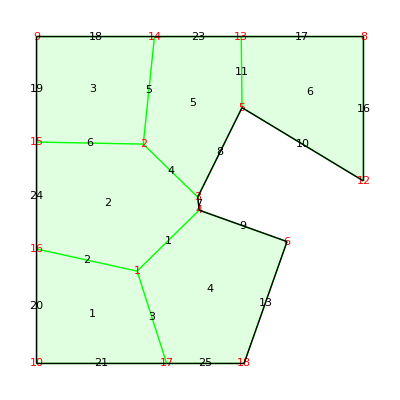

```mathematica
R=DeleteCell[Q, 5];
R=DeleteCell[R, 7];
S=DTissue2Tissue[R];
map=ShowTissue[S, "CellNumbers"-> True, "EdgeStyles"-> Directive[Green,Thick],"EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

## Find the outward vectors from each vertex on the boundary

```mathematica
VerticesOnBoundary[S]
```

{3,4,6,18,17,10,16,15,9,14,13,8,12,5}

```mathematica
VON=VertexOutwardVector[S,#, True]&/@VerticesOnBoundary[S]
```

{{0.524939,-0.469138},{0.429789,0.453784},{0.849204,0.528066},{0.416288,-0.909233},{0.163321,-0.707842},{-0.747623,-0.664123},{-0.744211,0.107072},{-0.745263,-0.0194293},{-0.732646,0.68061},{0.130895,0.757251},{-0.0930399,0.721279},{0.694718,0.719283},{0.520579,-0.853814},{0.010138,-0.156034}}

```mathematica
CVC=TissueVertices[S][[VerticesOnBoundary[S]]]
```

{{-0.692396,0.884224},{-0.249838,-3.10607},{26.6208,-12.7264},{13.4724,-50.},{-10.1955,-50.},{-50,-50},{-50.,-14.9773},{-50.,17.7221},{-50,50},{-13.9243,50.},{12.6075,50.},{50,50},{50.,5.82435},{12.858,28.2505}}

#### figure out a good number for the length of the vector

```mathematica
len = .5 * EdgeLengths[S]//Mean
```

15.3626

Observe that the outward vector is nto really normal - it depends on the shape of the nearby tissue boundary.

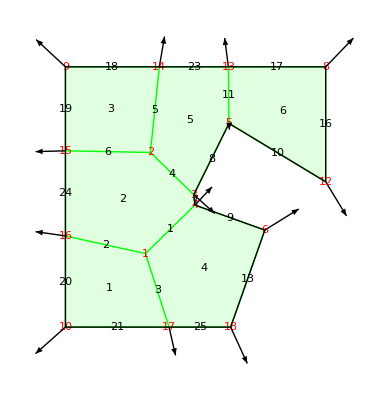

```mathematica
Show[map,Graphics[MapThread[Arrow[{#1,#1+len*#2}]&, {CVC, VON}]]]
```